```mathematica
<<SVG`
```

```mathematica
?SVG`*
```

SVG`ExportSVG

ExportSVG[SVG`Private`gr:Blank[Graphics]]:=SVG`Private`distributeDirectives[First[SVG`Private`gr]]

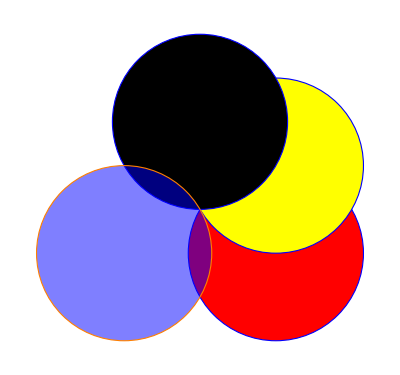

```mathematica
gr=Graphics[{EdgeForm[Directive[Dashed,Blue,Thick]],{Red,Disk[#],{Yellow,Disk[#+{0,1}]}},Disk[#2],{Blue,EdgeForm@Orange,FaceForm@Opacity@.5,Disk[#3]}}&@@CirclePoints[3]]
```

```mathematica
ExportSVG@gr
```

{{GrayLevel[0],EdgeForm[Directive[Dashing[{Small,Small}],RGBColor[0, 0, 1],Thickness[Large]]],RGBColor[1, 0, 0],Disk[{(√3)/2,-1/2}]},{GrayLevel[0],EdgeForm[Directive[Dashing[{Small,Small}],RGBColor[0, 0, 1],Thickness[Large]]],RGBColor[1, 0, 0],RGBColor[1, 1, 0],Disk[{(√3)/2,1/2}]},{GrayLevel[0],EdgeForm[Directive[Dashing[{Small,Small}],RGBColor[0, 0, 1],Thickness[Large]]],Disk[{0,1}]},{GrayLevel[0],EdgeForm[Directive[Dashing[{Small,Small}],RGBColor[0, 0, 1],Thickness[Large]]],RGBColor[0, 0, 1],EdgeForm[RGBColor[1, 0.5, 0]],FaceForm[Opacity[0.5]],Disk[{-(√3)/2,-1/2}]}}